# International Interaction Game

## Quantum-like Signorino’s Backward Induction Model

Quantum Extension of Signorino’s International Interaction Game Model

### Quantum-like Backward Induction Functions

```mathematica
(*Quantum Extension of Signorino's International Interaction Game Model Based on the classical implementation in signorino_model.m*)(*Quantum Backward Induction Functions*)(*Corrected Quantum Backward Induction Functions*)(*The key fix:Use amplitudes directly in utility calculations,not amplitude*Conjugate[amplitude]*)(*Quantum Extension of Signorino's International Interaction Game Model Based on the classical implementation in signorino_model.m*)(*Quantum Backward Induction Functions*)q10quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq10quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

q11quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq11quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

p8quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp8quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

p12quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notp12quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

q9quantum[theta1_,theta2_,U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1;
numerator=Exp[l2*UP2N12];
denominator=Exp[l2*UP2N12]+Exp[l2*U2Nego];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq9quantum[theta1_,theta2_,U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1;
numerator=Exp[l2*UP2N12];
denominator=Exp[l2*UP2N12]+Exp[l2*U2Nego];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

p7quantum[theta1_,theta2_,U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2;
numerator=Exp[l1*UP1N11];
denominator=Exp[l1*UP1N11]+Exp[l1*U1Nego];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notp7quantum[theta1_,theta2_,U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2;
numerator=Exp[l1*UP1N11];
denominator=Exp[l1*UP1N11]+Exp[l1*U1Nego];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

q6quantum[theta1_,theta2_,U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p8val,p7val,notp7val,notp8val,UP2N8,q11val,notq11val,U2N11,UP2N7,numerator,denominator,exponentialFactor},p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
U2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP2N7=p7val*Conjugate[p7val]*U2N11+notp7val*Conjugate[notp7val]*U2Nego;
numerator=Exp[l2*UP2N8];
denominator=Exp[l2*UP2N8]+Exp[l2*UP2N7];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq6quantum[theta1_,theta2_,U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p8val,p7val,notp7val,notp8val,UP2N8,q11val,notq11val,U2N11,UP2N7,numerator,denominator,exponentialFactor},p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
U2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP2N7=p7val*Conjugate[p7val]*U2N11+notp7val*Conjugate[notp7val]*U2Nego;
numerator=Exp[l2*UP2N8];
denominator=Exp[l2*UP2N8]+Exp[l2*UP2N7];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

p5quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q10val,notq10val,UP1N10,q9val,notq9val,UP1N9,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*Conjugate[p12val]*U1War2+notp12val*Conjugate[notp12val]*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego;
numerator=Exp[l1*UP1N10];
denominator=Exp[l1*UP1N10]+Exp[l1*UP1N9];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notp5quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q10val,notq10val,UP1N10,q9val,notq9val,UP1N9,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*Conjugate[p12val]*U1War2+notp12val*Conjugate[notp12val]*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego;
numerator=Exp[l1*UP1N10];
denominator=Exp[l1*UP1N10]+Exp[l1*UP1N9];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

p4quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,p8val,notp8val,UP1N8,p7val,notp7val,UP1N7,q6val,notq6val,UP1N6,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7;
numerator=Exp[l1*UP1N6];
denominator=Exp[l1*UP1N6]+Exp[l1*U1Acq1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notp4quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,p8val,notp8val,UP1N8,p7val,notp7val,UP1N7,q6val,notq6val,UP1N6,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7;
numerator=Exp[l1*UP1N6];
denominator=Exp[l1*UP1N6]+Exp[l1*U1Acq1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

q3quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,q10val,notq10val,UP2N10,q9val,notq9val,UP2N9,p5val,notp5val,UP2N5,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N10=q10val*Conjugate[q10val]*U2War1+notq10val*Conjugate[notq10val]*U2Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP2N9=q9val*Conjugate[q9val]*UP2N12+notq9val*Conjugate[notq9val]*U2Nego;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP2N5=p5val*Conjugate[p5val]*UP2N10+notp5val*Conjugate[notp5val]*UP2N9;
numerator=Exp[l2*UP2N5];
denominator=Exp[l2*UP2N5]+Exp[l2*U2Acq2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq3quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,q10val,notq10val,UP2N10,q9val,notq9val,UP2N9,p5val,notp5val,UP2N5,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N10=q10val*Conjugate[q10val]*U2War1+notq10val*Conjugate[notq10val]*U2Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP2N9=q9val*Conjugate[q9val]*UP2N12+notq9val*Conjugate[notq9val]*U2Nego;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP2N5=p5val*Conjugate[p5val]*UP2N10+notp5val*Conjugate[notp5val]*UP2N9;
numerator=Exp[l2*UP2N5];
denominator=Exp[l2*UP2N5]+Exp[l2*U2Acq2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

q2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP2N11,p7val,notp7val,UP2N7,p8val,notp8val,UP2N8,q6val,notq6val,UP2N6,p4val,notp4val,UP2N4,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP2N7=p7val*Conjugate[p7val]*UP2N11+notp7val*Conjugate[notp7val]*U2Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP2N6=q6val*Conjugate[q6val]*UP2N8+notq6val*Conjugate[notq6val]*UP2N7;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP2N4=p4val*Conjugate[p4val]*UP2N6+notp4val*Conjugate[notp4val]*U2Acq1;
numerator=Exp[l2*UP2N4];
denominator=Exp[l2*UP2N4]+Exp[l2*U2SQ];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP2N11,p7val,notp7val,UP2N7,p8val,notp8val,UP2N8,q6val,notq6val,UP2N6,p4val,notp4val,UP2N4,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP2N7=p7val*Conjugate[p7val]*UP2N11+notp7val*Conjugate[notp7val]*U2Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP2N6=q6val*Conjugate[q6val]*UP2N8+notq6val*Conjugate[notq6val]*UP2N7;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP2N4=p4val*Conjugate[p4val]*UP2N6+notp4val*Conjugate[notp4val]*U2Acq1;
numerator=Exp[l2*UP2N4];
denominator=Exp[l2*UP2N4]+Exp[l2*U2SQ];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];



p1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q11val,notq11val,UP1N11,q9val,notq9val,UP1N9,p7val,notp7val,UP1N7,p8val,notp8val,UP1N8,q10val,notq10val,UP1N10,q6val,notq6val,UP1N6,p5val,notp5val,UP1N5,p4val,notp4val,UP1N4,q3val,notq3val,UP1N3,q2val,notq2val,UP1N2,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*Conjugate[p12val]*U1War2+notp12val*Conjugate[notp12val]*U1Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP1N5=p5val*Conjugate[p5val]*UP1N10+notp5val*Conjugate[notp5val]*UP1N9;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP1N4=p4val*Conjugate[p4val]*UP1N6+notp4val*Conjugate[notp4val]*U1Acq1;
q3val=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notq3val=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
UP1N3=q3val*Conjugate[q3val]*UP1N5+notq3val*Conjugate[notq3val]*U1Acq2;
q2val=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notq2val=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
UP1N2=q2val*Conjugate[q2val]*UP1N4+notq2val*Conjugate[notq2val]*U1SQ;
numerator=Exp[l1*UP1N3];
denominator=Exp[l1*UP1N3]+Exp[l1*UP1N2];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notp1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q11val,notq11val,UP1N11,q9val,notq9val,UP1N9,p7val,notp7val,UP1N7,p8val,notp8val,UP1N8,q10val,notq10val,UP1N10,q6val,notq6val,UP1N6,p5val,notp5val,UP1N5,p4val,notp4val,UP1N4,q3val,notq3val,UP1N3,q2val,notq2val,UP1N2,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*Conjugate[p12val]*U1War2+notp12val*Conjugate[notp12val]*U1Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP1N5=p5val*Conjugate[p5val]*UP1N10+notp5val*Conjugate[notp5val]*UP1N9;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP1N4=p4val*Conjugate[p4val]*UP1N6+notp4val*Conjugate[notp4val]*U1Acq1;
q3val=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notq3val=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
UP1N3=q3val*Conjugate[q3val]*UP1N5+notq3val*Conjugate[notq3val]*U1Acq2;
q2val=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notq2val=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
UP1N2=q2val*Conjugate[q2val]*UP1N4+notq2val*Conjugate[notq2val]*U1SQ;
numerator=Exp[l1*UP1N3];
denominator=Exp[l1*UP1N3]+Exp[l1*UP1N2];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]
```

### Outcome Functions

```mathematica
SQquantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,notq2,res},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notq2=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
(notp1*notq2)*Conjugate[(notp1*notq2)]
];

ACQ1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,notp4},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notp4=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
(notp1*q2*notp4)*Conjugate[notp1*q2*notp4]
];

ACQ2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p1,notq3},p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notq3=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
(p1*notq3)*Conjugate[p1*notq3]
];

NEGOquantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p1,notp1,q2,q3,p4,notp5,notq6,notp7,notq9},p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notp7=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notq9=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
(notp1*q2*p4*notq6*notp7+p1*q3*notp5*notq9)*Conjugate[notp1*q2*p4*notq6*notp7+p1*q3*notp5*notq9]
];

CAP1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,p4,q6,notp8,p1,q3,notp5,q9,notp12},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
q6=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notp8=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
q9=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notp12=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
(notp1*q2*p4*q6*notp8+p1*q3*notp5*q9*notp12)*Conjugate[notp1*q2*p4*q6*notp8+p1*q3*notp5*q9*notp12]
];

CAP2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,p4,notq6,p7,notq11,p1,q3,p5,notq10},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
p7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notq11=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
p5=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notq10=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
(notp1*q2*p4*notq6*p7*notq11+p1*q3*p5*notq10)*Conjugate[notp1*q2*p4*notq6*p7*notq11+p1*q3*p5*notq10]
];

WAR1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,p1,q2,p4,notq6,p7,q11,q3,q10,p5},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
p7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
q11=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
q10=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
p5=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
(notp1*q2*p4*notq6*p7*q11+p1*q3*p5*q10)*Conjugate[(notp1*q2*p4*notq6*p7*q11+p1*q3*p5*q10)]
];

WAR2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,p1,q2,p4,q6,p8,q3,notp5,q9,p12},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
q6=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
p8=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
q9=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
p12=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
(notp1*q2*p4*q6*p8+p1*q3*notp5*q9*p12)*Conjugate[notp1*q2*p4*q6*p8+p1*q3*notp5*q9*p12]
];
```

### Aux Functions

#### calculateQuantumOutcome

```mathematica
calculateQuantumOutcome[data_,rowIndex_Integer,theta1_:0,theta2_:0,l1_:1,l2_:1]:=Module[{utils,quantumAmplitudes,finalProbabilities,outcomes,outcomeProbs,maxVal,maxOutcomes,prediction,roundedProbs},

utils=extractUtilities[data,rowIndex];
If[utils===$Failed,
Return[$Failed]];

(*Compute quantum probability amplitudes*)
quantumAmplitudes=
Quiet[{
SQquantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],
utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],
utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],
utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

ACQ1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],
utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],
utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],
utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

ACQ2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

NEGOquantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

CAP1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

CAP2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

WAR1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

WAR2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2]
}];

(*Calculate final probabilities directly from amplitudes*)
finalProbabilities=Abs[#]^2&/@quantumAmplitudes;

(*Normalize probabilities*)
finalProbabilities=finalProbabilities/Total[finalProbabilities];

outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1","WAR2"};

(*Create outcome probabilities association for prediction*)
outcomeProbs=Association[MapThread[Rule,{outcomes,finalProbabilities}]];

(*Round probabilities to 4 decimal places for comparison*)
roundedProbs=Association[#->Round[outcomeProbs[#],0.0001]&/@Keys[outcomeProbs]];
maxVal=Max[Values[roundedProbs]];
maxOutcomes=Keys[Select[roundedProbs,#==maxVal&]];
(*Randomly select one if there are ties*)
prediction=RandomChoice[maxOutcomes];

Association[
"SQ"->finalProbabilities[[1]],
"ACQ1"->finalProbabilities[[2]],
"ACQ2"->finalProbabilities[[3]],
"NEGO"->finalProbabilities[[4]],
"CAP1"->finalProbabilities[[5]],
"CAP2"->finalProbabilities[[6]],
"WAR1"->finalProbabilities[[7]],
"WAR2"->finalProbabilities[[8]],
"prediction"->prediction,
"groundtruth"->utils["groundtruth"],
"utilities"->utils,
"theta1"->theta1,
"theta2"->theta2,
"l1"->l1,"l2"->l2,
"total"->Total[finalProbabilities]]]
```

#### getFirstNEntries

```mathematica
getFirstNEntries[resultAllData_,N_Integer]:=Module[{extractedEntries},
(*Input validation*)
If[!ListQ[resultAllData],
Print["Error: resultAllData must be a list"];
Return[$Failed]
];

If[N<=0,
Print["Error: N must be a positive integer"];
Return[$Failed]
];

If[Length[resultAllData]==0,
Print["Warning: resultAllData is empty"];
Return[{}]
];

(*Extract only the specified components from each entry*)
extractedEntries=
Table[Module[{entry,utils},
entry=resultAllData[[i]];
utils=If[KeyExistsQ[entry,"utilities"],entry["utilities"],Association[]];

Association[
"SQ"->If[KeyExistsQ[entry,"SQ"],Round[entry["SQ"],0.0001],0],
"ACQ1"->If[KeyExistsQ[entry,"ACQ1"],Round[entry["ACQ1"],0.0001],0],
"ACQ2"->If[KeyExistsQ[entry,"ACQ2"],Round[entry["ACQ2"],0.0001],0],
"NEGO"->If[KeyExistsQ[entry,"NEGO"],Round[entry["NEGO"],0.0001],0],
"CAP1"->If[KeyExistsQ[entry,"CAP1"],Round[entry["CAP1"],0.0001],0],
"CAP2"->If[KeyExistsQ[entry,"CAP2"],Round[entry["CAP2"],0.0001],0],
"WAR1"->If[KeyExistsQ[entry,"WAR1"],Round[entry["WAR1"],0.0001],0],
"WAR2"->If[KeyExistsQ[entry,"WAR2"],Round[entry["WAR2"],0.0001],0],
"prediction"->If[KeyExistsQ[entry,"prediction"],entry["prediction"],"UNKNOWN"],
"groundtruth"->If[KeyExistsQ[entry,"groundtruth"],entry["groundtruth"],"UNKNOWN"],
"Agent1"->If[KeyExistsQ[utils,"Agent1"],utils["Agent1"],"UNKNOWN"],
"Agent2"->If[KeyExistsQ[utils,"Agent2"],utils["Agent2"],"UNKNOWN"]]
],{i,Min[N,Length[resultAllData]]}
];

(*Return extracted entries with informative message*)
If[N>=Length[resultAllData],
Print["Note: Requested ",N," entries but only ",Length[resultAllData]," available. Returning all entries with extracted components."];
Return[extractedEntries],
Print["Returning first ",N," entries out of ",Length[resultAllData]," total entries with extracted components."];
Return[extractedEntries]]]
```

#### processQuantumDataset

```mathematica
(*Process Quantum Dataset*)
processQuantumDataset[data_,theta1_:0,theta2_:0,l1_:1,l2_:1]:=Module[{results,i},If[data===$Failed,Print["Error: Invalid data passed to processQuantumDataset"];
Return[{}]];
Print["Processing ",data["nrows"]," rows with quantum model..."];
Print["Parameters: θ1=",theta1,", θ2=",theta2,", λ1=",l1,", λ2=",l2];
results={};
Do[Module[{result},If[Mod[i,50]==0,Print["Processing row ",i,"/",data["nrows"]]];
result=calculateQuantumOutcome[data,i,theta1,theta2,l1,l2];
If[result=!=$Failed,AppendTo[results,result],Print["Warning: Failed to process row ",i]]],{i,1,data["nrows"]}];
Print["Successfully processed ",Length[results]," out of ",data["nrows"]," rows"];
results]
```

#### calculateQuantumAccuracy

```mathematica
calculateQuantumAccuracy[results_]:=Module[{predTruth,correct},
If[Length[results]==0,Print["Warning: No results to calculate accuracy from"];
Return[0]
];

predTruth=extractPredictionsAndGroundtruth[results];

If[Length[predTruth["predictions"]]==0,Print["Warning: No valid predictions found"];
Return[0]
];

correct=MapThread[Equal,{predTruth["predictions"],predTruth["groundtruth"]}];
N[Count[correct,True]/Length[correct]]
]
```

#### plotQuantumConfusionMatrix

```mathematica
plotQuantumConfusionMatrix[results_,theta1_:0,theta2_:0,l1_:1,l2_:1,title_:"Quantum Confusion Matrix"]:=Module[{predictions,groundTruths,outcomes,confusionData,accuracy,predTruth},If[Length[results]==0,Print["Warning: No results provided for confusion matrix"];
Return[Null]];
predTruth=extractPredictionsAndGroundtruth[results];
predictions=predTruth["predictions"];
groundTruths=predTruth["groundtruth"];
If[Length[predictions]==0,Print["Warning: No valid predictions found"];
Return[Null]];
accuracy=N[Count[MapThread[Equal,{predictions,groundTruths}],True]/Length[results]];
outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1", "WAR2"};
confusionData=Table[Count[MapThread[List,{groundTruths,predictions}],{actualOutcome,predictedOutcome}],{actualOutcome,outcomes},{predictedOutcome,outcomes}];
Print[Style[title,16,Bold]];
Print[Style["θ1 = "<>ToString[theta1]<>" θ2 = "<>ToString[theta2]<>" λ1 = "<>ToString[l1]<>" λ2 = "<>ToString[l2]<>" | Accuracy = "<>ToString[N[accuracy]],14]];
Print[""];
Grid[Prepend[MapThread[Prepend,{confusionData,outcomes}],Prepend[outcomes,Style["Actual \\ Predicted",Bold]]],Frame->All,Alignment->Center,Background->{None,{LightBlue,None}},ItemStyle->{Automatic,{Bold,Automatic}},Spacings->{2,1},FrameStyle->Thick,Dividers->{{2->Thick},{2->Thick}}]]
```

#### loadData

```mathematica
loadData[filename_String]:=Module[{rawData,headers,dataRows,groundtruth,utilityData,cleanedData,requiredColumns,missingColumns},

Print["Loading CSV file: ",filename];
rawData=Import[filename,"CSV"];

If[Head[rawData]=!=List||Length[rawData]<2,
Print["Error: Could not load CSV file or file is empty"];
Return[$Failed]
];

headers=First[rawData];
dataRows=Rest[rawData];

Print["Loaded ",Length[dataRows]," rows with ",Length[headers]," columns"];
cleanedData=Map[Function[row,Map[Function[cell,If[NumericQ[cell],cell,If[StringQ[cell]&&StringMatchQ[cell,NumberString],ToExpression[cell],cell]]],row]],dataRows];
groundtruth=cleanedData[[All,-1]];

utilityData=Association[Table[headers[[i]]->cleanedData[[All,i]],{i,Length[headers]}]];

requiredColumns={"wrTu1wr2","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1neg","wrTu1ac1","wrTu1ac2","wrTu1sq","wrTu2wr2","wrTu2cp1","wrTu2wr1","wrTu2cp2","wrTu2neg","wrTu2ac1","wrTu2ac2","wrTu2sq"};
missingColumns=Select[requiredColumns,!KeyExistsQ[utilityData,#]&];

If[Length[missingColumns]>0,
Print["Warning: Missing required columns: ",missingColumns];
];

Association[
"groundtruth"->groundtruth,
"data"->utilityData,
"nrows"->Length[cleanedData],
"headers"->headers,
"filename"->filename]
]
```

#### extractUtilities

```mathematica
extractUtilities[data_,rowIndex_Integer]:=Module[{row,utils},
If[rowIndex<1||rowIndex>data["nrows"],
Print["Error: Row index ",rowIndex," out of range [1, ",data["nrows"],"]"];
Return[$Failed]
];

row=data["data"];
utils=Association[];

(*Player 1 utilities*)
utils["U1War2"]=If[KeyExistsQ[row,"wrTu1wr2"]&&NumericQ[row["wrTu1wr2"][[rowIndex]]],row["wrTu1wr2"][[rowIndex]],0.0];
utils["U1Cap1"]=If[KeyExistsQ[row,"wrTu1cp1"]&&NumericQ[row["wrTu1cp1"][[rowIndex]]],row["wrTu1cp1"][[rowIndex]],0.0];
utils["U1Cap2"]=If[KeyExistsQ[row,"wrTu1cp2"]&&NumericQ[row["wrTu1cp2"][[rowIndex]]],row["wrTu1cp2"][[rowIndex]],0.0];
utils["U1War1"]=If[KeyExistsQ[row,"wrTu1wr1"]&&NumericQ[row["wrTu1wr1"][[rowIndex]]],row["wrTu1wr1"][[rowIndex]],0.0];
utils["U1Nego"]=If[KeyExistsQ[row,"wrTu1neg"]&&NumericQ[row["wrTu1neg"][[rowIndex]]],row["wrTu1neg"][[rowIndex]],0.0];
utils["U1Acq1"]=If[KeyExistsQ[row,"wrTu1ac1"]&&NumericQ[row["wrTu1ac1"][[rowIndex]]],row["wrTu1ac1"][[rowIndex]],0.0];
utils["U1Acq2"]=If[KeyExistsQ[row,"wrTu1ac2"]&&NumericQ[row["wrTu1ac2"][[rowIndex]]],row["wrTu1ac2"][[rowIndex]],0.0];
utils["U1SQ"]=If[KeyExistsQ[row,"wrTu1sq"]&&NumericQ[row["wrTu1sq"][[rowIndex]]],row["wrTu1sq"][[rowIndex]],0.0];

(*Player 2 utilities*)
utils["U2War2"]=If[KeyExistsQ[row,"wrTu2wr2"]&&NumericQ[row["wrTu2wr2"][[rowIndex]]],row["wrTu2wr2"][[rowIndex]],0.0];
utils["U2Cap1"]=If[KeyExistsQ[row,"wrTu2cp1"]&&NumericQ[row["wrTu2cp1"][[rowIndex]]],row["wrTu2cp1"][[rowIndex]],0.0];
utils["U2War1"]=If[KeyExistsQ[row,"wrTu2wr1"]&&NumericQ[row["wrTu2wr1"][[rowIndex]]],row["wrTu2wr1"][[rowIndex]],0.0];
utils["U2Cap2"]=If[KeyExistsQ[row,"wrTu2cp2"]&&NumericQ[row["wrTu2cp2"][[rowIndex]]],row["wrTu2cp2"][[rowIndex]],0.0];
utils["U2Nego"]=If[KeyExistsQ[row,"wrTu2neg"]&&NumericQ[row["wrTu2neg"][[rowIndex]]],row["wrTu2neg"][[rowIndex]],0.0];
utils["U2Acq1"]=If[KeyExistsQ[row,"wrTu2ac1"]&&NumericQ[row["wrTu2ac1"][[rowIndex]]],row["wrTu2ac1"][[rowIndex]],0.0];
utils["U2Acq2"]=If[KeyExistsQ[row,"wrTu2ac2"]&&NumericQ[row["wrTu2ac2"][[rowIndex]]],row["wrTu2ac2"][[rowIndex]],0.0];
utils["U2SQ"]=If[KeyExistsQ[row,"wrTu2sq"]&&NumericQ[row["wrTu2sq"][[rowIndex]]],row["wrTu2sq"][[rowIndex]],0.0];
utils["Agent1"]=If[KeyExistsQ[row,"ISOShNm1"],row["ISOShNm1"][[rowIndex]],"Unknown"];
utils["Agent2"]=If[KeyExistsQ[row,"ISOShNm2"],row["ISOShNm2"][[rowIndex]],"Unknown"];

(*Additional information*)
utils["groundtruth"]=data["groundtruth"][[rowIndex]];
utils["ccode1"]=If[KeyExistsQ[row,"ccode1"]&&NumericQ[row["ccode1"][[rowIndex]]],row["ccode1"][[rowIndex]],0];
utils["ccode2"]=If[KeyExistsQ[row,"ccode2"]&&NumericQ[row["ccode2"][[rowIndex]]],row["ccode2"][[rowIndex]],0];
utils["year"]=If[KeyExistsQ[row,"year"]&&NumericQ[row["year"][[rowIndex]]],row["year"][[rowIndex]],0];
utils]
```

#### extractPredictionsAndGroundtruth

```mathematica
extractPredictionsAndGroundtruth[results_]:=Module[{predictions,groundTruth,outcomes},
outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1", "WAR2"};
predictions=
Table[
Module[{outcomeProbs,maxVal,maxOutcome},
outcomeProbs=
Association[
"ACQ1"->If[KeyExistsQ[results[[i]],"ACQ1"]&&NumericQ[results[[i]]["ACQ1"]],results[[i]]["ACQ1"],0],
"ACQ2"->If[KeyExistsQ[results[[i]],"ACQ2"]&&NumericQ[results[[i]]["ACQ2"]],results[[i]]["ACQ2"],0],
"CAP1"->If[KeyExistsQ[results[[i]],"CAP1"]&&NumericQ[results[[i]]["CAP1"]],results[[i]]["CAP1"],0],
"CAP2"->If[KeyExistsQ[results[[i]],"CAP2"]&&NumericQ[results[[i]]["CAP2"]],results[[i]]["CAP2"],0],
"NEGO"->If[KeyExistsQ[results[[i]],"NEGO"]&&NumericQ[results[[i]]["NEGO"]],results[[i]]["NEGO"],0],
"SQ"->If[KeyExistsQ[results[[i]],"SQ"]&&NumericQ[results[[i]]["SQ"]],results[[i]]["SQ"],0],
"WAR1"->If[KeyExistsQ[results[[i]],"WAR1"]&&NumericQ[results[[i]]["WAR1"]],results[[i]]["WAR1"],0],
"WAR2"->If[KeyExistsQ[results[[i]],"WAR2"]&&NumericQ[results[[i]]["WAR2"]],results[[i]]["WAR2"],0]
];

(*Find outcome with maximum probability*)
maxVal=Max[Values[outcomeProbs]];
maxOutcome=First[Keys[Select[outcomeProbs,#==maxVal&]]];
maxOutcome],{i,Length[results]}];

groundTruth=Table[If[KeyExistsQ[results[[i]],"groundtruth"],results[[i]]["groundtruth"],"UNKNOWN"],{i,Length[results]}];
Association[
"predictions"->predictions,
"groundtruth"->groundTruth]]
```

### Optimization Functions

```mathematica
(*Grid Search Function for Optimal Theta Parameters*)
gridSearchQuantumThetas[data_,theta1Range_List,theta2Range_List,l1_:1,l2_:1,verbose_:True]:=Module[{results,bestAccuracy,bestTheta1,bestTheta2,totalCombinations,currentCombination,startTime,gridResults,theta1Values,theta2Values},

(*Input validation*)If[data===$Failed||!KeyExistsQ[data,"nrows"],Print["Error: Invalid data provided"];
Return[$Failed]];

(*Extract theta values from ranges*)
theta1Values=theta1Range;
theta2Values=theta2Range;
totalCombinations=Length[theta1Values]*Length[theta2Values];
currentCombination=0;
bestAccuracy=0;
bestTheta1=First[theta1Values];
bestTheta2=First[theta2Values];
If[verbose,
Print["Starting grid search over ",totalCombinations," parameter combinations..."];
Print["Theta1 range: ",theta1Values];
Print["Theta2 range: ",theta2Values];
Print["Lambda1 = ",l1,", Lambda2 = ",l2];
Print["Dataset size: ",data["nrows"]," rows"];
Print[""];
];

startTime=AbsoluteTime[];
gridResults={};

(*Grid search loop*)Do[Module[{currentResults,currentAccuracy,elapsedTime,estimatedTotal,estimatedRemaining},currentCombination++;
If[verbose&&Mod[currentCombination,Max[1,Floor[totalCombinations/20]]]==0,elapsedTime=AbsoluteTime[]-startTime;
estimatedTotal=elapsedTime*totalCombinations/currentCombination;
estimatedRemaining=estimatedTotal-elapsedTime;
Print["Progress: ",currentCombination,"/",totalCombinations," (",N[100*currentCombination/totalCombinations,3],"%)"];
Print["Elapsed: ",N[elapsedTime/60,2]," min, Estimated remaining: ",N[estimatedRemaining/60,2]," min"];
Print["Current best: θ1=",bestTheta1,", θ2=",bestTheta2,", Accuracy=",N[bestAccuracy,4]];
Print[""];]
;
(*Calculate results for current theta combination*)currentResults=Quiet[processQuantumDataset[data,theta1,theta2,l1,l2]];
If[Length[currentResults]>0,
currentAccuracy=calculateQuantumAccuracy[currentResults];

(*Store result*)
AppendTo[gridResults,
Association["theta1"->theta1,"theta2"->theta2,"accuracy"->currentAccuracy,"l1"->l1,"l2"->l2]
];

(*Update best parameters if current is better*)If[currentAccuracy>bestAccuracy,
bestAccuracy=currentAccuracy;
bestTheta1=theta1;
bestTheta2=theta2;

If[verbose,
Print["New best found: θ1=",theta1,", θ2=",theta2,", Accuracy=",N[currentAccuracy,4]];
];
];,

(*Handle failed calculation*)
If[verbose,
Print["Warning: Failed to calculate results for θ1=",theta1,", θ2=",theta2];
];
AppendTo[gridResults,
Association["theta1"->theta1,"theta2"->theta2,"accuracy"->0,"l1"->l1,"l2"->l2,"failed"->True]
];
];
],
{theta1,theta1Values},{theta2,theta2Values}
];

If[verbose,
Print["Grid search completed!"];
Print["Total time: ",N[(AbsoluteTime[]-startTime)/60,2]," minutes"];
Print["Best parameters found:"];
Print["  θ1 = ",bestTheta1];
Print["  θ2 = ",bestTheta2];
Print["  Accuracy = ",N[bestAccuracy,4]];
Print[""];
];

(*Return comprehensive results*)Association["bestTheta1"->bestTheta1,
"bestTheta2"->bestTheta2,
"bestAccuracy"->bestAccuracy,
"allResults"->gridResults,
"totalCombinations"->totalCombinations,
"l1"->l1,"l2"->l2]
]

(*Helper function to create parameter ranges*)
createThetaRange[min_,max_,steps_]:=
If[steps==1,
{min},
Range[min,max,(max-min)/(steps-1)]
]

(*Function to visualize grid search results*)
visualizeGridSearchResults[gridSearchResults_]:=Module[{validResults,heatmapData,theta1Values,theta2Values,accuracyMatrix,minAcc,maxAcc,tickLabels1,tickLabels2,theta1Ticks,theta2Ticks,bestIndex,plot},

(*Check if this is a proper grid search result structure*)If[!AssociationQ[gridSearchResults]||!KeyExistsQ[gridSearchResults,"allResults"],Print["Error: Input must be a grid search results Association with 'allResults' key"];
Print["Use gridSearchQuantumThetas[] to generate proper grid search results"];
Return[Null];];
validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
If[Length[validResults]==0,Print["No valid results to visualize"];
Return[Null];];
theta1Values=Sort[DeleteDuplicates[#["theta1"]&/@validResults]];
theta2Values=Sort[DeleteDuplicates[#["theta2"]&/@validResults]];

(*Create accuracy matrix for heatmap*)accuracyMatrix=Table[Module[{matchingResult},matchingResult=SelectFirst[validResults,#["theta1"]==theta1&&#["theta2"]==theta2&];
If[matchingResult===Missing["NotFound"],0,matchingResult["accuracy"]]],{theta1,theta1Values},{theta2,theta2Values}];
(*Calculate min/max for better color scaling*)minAcc=Min[Flatten[accuracyMatrix]];
maxAcc=Max[Flatten[accuracyMatrix]];
(*Create proper tick labels*)tickLabels1=Table[{i,NumberForm[N[theta1Values[[i]],3],{4,3}]},{i,Length[theta1Values]}];
tickLabels2=Table[{i,NumberForm[N[theta2Values[[i]],3],{4,3}]},{i,Length[theta2Values]}];
(*Find position of best result for highlighting*)bestIndex=Position[accuracyMatrix,maxAcc];
Print[Style["Grid Search Results Visualization",16,Bold]];
Print[Style[StringJoin["Parameter Space: ",ToString[Length[theta1Values]]," × ",ToString[Length[theta2Values]]," = ",ToString[Length[validResults]]," combinations"],14]];
Print[Style[StringJoin["Best Parameters: θ₁ = ",ToString[NumberForm[N[gridSearchResults["bestTheta1"],4],{5,4}]],", θ₂ = ",ToString[NumberForm[N[gridSearchResults["bestTheta2"],4],{5,4}]]," → Accuracy = ",ToString[NumberForm[N[gridSearchResults["bestAccuracy"],4],{5,4}]]," (",ToString[NumberForm[100*N[gridSearchResults["bestAccuracy"]],{5,2}]],"%)"],14,RGBColor[0.1,0.5,0.1]]];
Print[Style[StringJoin["Accuracy Range: ",ToString[NumberForm[N[minAcc],{4,3}]]," - ",ToString[NumberForm[N[maxAcc],{4,3}]]],12,Gray]];
Print[""];
(*Create improved heatmap*)plot=ArrayPlot[Transpose[accuracyMatrix],(*Professional color scheme*)ColorFunction->(Blend[{RGBColor[0.2,0.2,0.4],(*Dark blue for low values*)RGBColor[0.3,0.6,0.8],(*Medium blue*)RGBColor[0.9,0.9,0.3],(*Yellow for medium values*)RGBColor[0.9,0.6,0.1],(*Orange*)RGBColor[0.8,0.2,0.2]     (*Red for high values*)},#]&),ColorFunctionScaling->True,(*Proper labels and ticks*)PlotLabel->Style["Parameter Optimization Heatmap",16,Bold],FrameLabel->{Style["θ₁ (Player 1 Quantum Phase)",14,Bold],Style["θ₂ (Player 2 Quantum Phase)",14,Bold]},(*Custom ticks with actual parameter values*)FrameTicks->{{tickLabels2,None},(*Bottom ticks for theta2*){tickLabels1,None}   (*Left ticks for theta1*)},(*Plot options*)AspectRatio->Automatic,ImageSize->{500,400},Frame->True,FrameStyle->Black,PlotRangePadding->None,(*Color bar legend*)PlotLegends->Placed[BarLegend[{Blend[{RGBColor[0.2,0.2,0.4],RGBColor[0.3,0.6,0.8],RGBColor[0.9,0.9,0.3],RGBColor[0.9,0.6,0.1],RGBColor[0.8,0.2,0.2]},#]&,{minAcc,maxAcc}},LegendLabel->Style["Accuracy",12,Bold],LegendMarkerSize->200],Right]];
(*Add text annotations for best points if there are few enough points*)If[Length[validResults]<=25,plot=Show[plot,Graphics[{White,EdgeForm[{Thick,Black}],Table[Module[{acc,pos1,pos2},acc=accuracyMatrix[[i,j]];
pos1=j;pos2=i;
If[acc==maxAcc,{Red,EdgeForm[{Thick,Red}],Rectangle[{pos1-0.4,pos2-0.4},{pos1+0.4,pos2+0.4}]},If[acc>0.8*maxAcc,Text[Style[NumberForm[acc,{3,3}],10,Bold,White],{pos1,pos2}],Text[Style[NumberForm[acc,{3,3}],9,Black],{pos1,pos2}]]]],{i,Length[theta1Values]},{j,Length[theta2Values]}]}]]];
(*Display summary statistics*)Print[Style["Summary Statistics:",14,Bold]];
Print["• Mean Accuracy: ",NumberForm[Mean[Flatten[accuracyMatrix]],{4,3}]];
Print["• Standard Deviation: ",NumberForm[StandardDeviation[Flatten[accuracyMatrix]],{4,3}]];
Print["• Improvement over Random: ",NumberForm[100*(maxAcc-1/7),{4,2}],"% points"];
plot]

(*Function to get top N parameter combinations*)
getTopParameterCombinations[gridSearchResults_,n_:5]:=Module[{validResults,sortedResults},validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
sortedResults=Reverse[SortBy[validResults,#["accuracy"]&]];
Take[sortedResults,Min[n,Length[sortedResults]]]]

(*For a focused search around your current parameters:*)
focusedSearchAroundCurrent[data_,currentTheta1_,currentTheta2_,rangeSize_:1.0,gridSize_:5]:=Module[{theta1Range,theta2Range,results},Print["Running focused search around θ1=",currentTheta1,", θ2=",currentTheta2];
theta1Range=createThetaRange[currentTheta1-rangeSize,currentTheta1+rangeSize,gridSize];
theta2Range=createThetaRange[currentTheta2-rangeSize,currentTheta2+rangeSize,gridSize];
Print["θ1 range: ",theta1Range];
Print["θ2 range: ",theta2Range];
results=gridSearchQuantumThetas[data,theta1Range,theta2Range,1,1,True];
Print["Focused search completed. Visualizing results..."];
visualizeGridSearchResults[results];
results]

(*Simple function to analyze current results *)analyzeCurrentResults[quantumResults_List]:=Module[{accuracy,sampleResult,theta1Val,theta2Val,predTruth},If[Length[quantumResults]==0,Print["No results to analyze"];
Return[$Failed];
];
(*Get sample result to extract theta values*)sampleResult=First[quantumResults];
theta1Val=sampleResult["theta1"];
theta2Val=sampleResult["theta2"];

(*Calculate accuracy*)accuracy=calculateQuantumAccuracy[quantumResults];

(*Get predictions and ground truth*)predTruth=extractPredictionsAndGroundtruth[quantumResults];
Print["=== Quantum Model Analysis ==="];
Print["Parameters: θ1 = ",N[theta1Val,4]," (",theta1Val,")"];
Print["           θ2 = ",N[theta2Val,4]," (",theta2Val,")"];
Print["Total cases: ",Length[quantumResults]];
Print["Accuracy: ",N[accuracy,4]," (",N[100*accuracy,2],"%)"];
Print[""];

(*Show outcome distribution*)Module[{outcomes,counts},outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1","WAR2"};
counts=Table[Count[predTruth["predictions"],outcome],{outcome,outcomes}];
Print["Prediction distribution:"];
Do[If[counts[[i]]>0,Print["  ",outcomes[[i]],": ",counts[[i]]," (",N[100*counts[[i]]/Length[predTruth["predictions"]],1],"%)"]],{i,Length[outcomes]}];];
Print[""];

(*Show confusion matrix*)plotQuantumConfusionMatrix[quantumResults,theta1Val,theta2Val,1,1,"Current Quantum Model Results"];
Association["accuracy"->accuracy,"theta1"->theta1Val,"theta2"->theta2Val,"totalCases"->Length[quantumResults],"predictions"->predTruth["predictions"],"groundTruth"->predTruth["groundtruth"]]]
```

## Experiments

### Debugging

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv"; 
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
u = extractUtilities[data, 1]
```

<|U1War2→-1.28132,U1Cap1→-1.86209,U1Cap2→1.42545,U1War1→-0.906611,U1Nego→-0.458194,U1Acq1→-1.11267,U1Acq2→1.49916,U1SQ→0.294146,U2War2→-0.089115,U2Cap1→1.2333,U2War1→-0.303673,U2Cap2→-1.60962,U2Nego→0.293366,U2Acq1→1.40122,U2Acq2→-1.1805,U2SQ→0.16449,Agent1→ESTONIA,Agent2→UNITED KINGDOM,groundtruth→SQ,ccode1→366,ccode2→200,year→1939|>

```mathematica
U1War2 = u["U1War2"];
U1War1 = u["U1War1"];
U1Acq1= u["U1Acq1"];
U1Acq2 = u["U1Acq2"];
U1Cap1 = u["U1Cap1"];
U1Cap2 = u["U1Cap2"];
U1Nego = u["U1Nego"];
U1SQ =      u["U1SQ"];

U2War2 = u["U2War2"];
U2War1 = u["U2War1"];
U2Acq1 = u["U2Acq1"];
U2Acq2 = u["U2Acq2"];
U2Cap1 = u["U2Cap1"];
U2Cap2 = u["U2Cap2"];
U2Nego = u["U2Nego"];
U2SQ = u["U2SQ"];
```

```mathematica
(*Continue your validation code*)(*Load data and extract utilities-your existing code*)datasetPath="D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
u=extractUtilities[data,1];
U1War2=u["U1War2"];
U1War1=u["U1War1"];
U1Acq1=u["U1Acq1"];
U1Acq2=u["U1Acq2"];
U1Cap1=u["U1Cap1"];
U1Cap2=u["U1Cap2"];
U1Nego=u["U1Nego"];
U1SQ=u["U1SQ"];
U2War2=u["U2War2"];
U2War1=u["U2War1"];
U2Acq1=u["U2Acq1"];
U2Acq2=u["U2Acq2"];
U2Cap1=u["U2Cap1"];
U2Cap2=u["U2Cap2"];
U2Nego=u["U2Nego"];
U2SQ=u["U2SQ"];

(*Validation function to check if quantum amplitude squared equals classical probability*)
validateQuantumClassical[quantumFunc_,classicalFunc_,args_,theta1_:Pi/2,theta2_:Pi/2]:=Module[{qVal,cVal,result},qVal=quantumFunc[theta1,theta2,Sequence@@args];
cVal=classicalFunc[Sequence@@args];
result=Abs[qVal]^2;
{quantumFunc,Abs[result-cVal]<10^(-10),result,cVal,Abs[result-cVal]}]

(*Test cases for terminal nodes (should be simplest)*)
Print["=== Testing Terminal Node Functions ==="];

(*q10 and notq10*)
test1=validateQuantumClassical[q10quantum,q10classical,{U2War1,U2Cap2,1,1}];
test2=validateQuantumClassical[notq10quantum,notq10classical,{U2War1,U2Cap2,1,1}];
Print["q10quantum: ",test1];
Print["notq10quantum: ",test2];

(*q11 and notq11*)
test3=validateQuantumClassical[q11quantum,q11classical,{U2War1,U2Cap2,1,1}];
test4=validateQuantumClassical[notq11quantum,notq11classical,{U2War1,U2Cap2,1,1}];
Print["q11quantum: ",test3];
Print["notq11quantum: ",test4];

(*p8 and notp8*)
test5=validateQuantumClassical[p8quantum,p8classical,{U1War2,U1Cap1,1,1}];
test6=validateQuantumClassical[notp8quantum,notp8classical,{U1War2,U1Cap1,1,1}];
Print["p8quantum: ",test5];
Print["notp8quantum: ",test6];

(*p12 and notp12*)
test7=validateQuantumClassical[p12quantum,p12classical,{U1War2,U1Cap1,1,1}];
test8=validateQuantumClassical[notp12quantum,notp12classical,{U1War2,U1Cap1,1,1}];
Print["p12quantum: ",test7];
Print["notp12quantum: ",test8];

Print["\n=== Testing Mid-Level Node Functions ==="];

(*q9 and notq9*)
test9=validateQuantumClassical[q9quantum,q9classical,{U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,1,1}];
test10=validateQuantumClassical[notq9quantum,notq9classical,{U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,1,1}];
Print["q9quantum: ",test9];
Print["notq9quantum: ",test10];

(*p7 and notp7*)
test11=validateQuantumClassical[p7quantum,p7classical,{U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,1,1}];
test12=validateQuantumClassical[notp7quantum,notp7classical,{U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,1,1}];
Print["p7quantum: ",test11];
Print["notp7quantum: ",test12];

(*q6 and notq6*)
test13=validateQuantumClassical[q6quantum,q6classical,{U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,1,1}];
test14=validateQuantumClassical[notq6quantum,notq6classical,{U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,1,1}];
Print["q6quantum: ",test13];
Print["notq6quantum: ",test14];

Print["\n=== Testing Complex Node Functions ==="];

(*p5 and notp5*)
test15=validateQuantumClassical[p5quantum,p5classical,{U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,1,1}];
test16=validateQuantumClassical[notp5quantum,notp5classical,{U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,1,1}];
Print["p5quantum: ",test15];
Print["notp5quantum: ",test16];

(*p4 and notp4*)
test17=validateQuantumClassical[p4quantum,p4classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,1,1}];
test18=validateQuantumClassical[notp4quantum,notp4classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,1,1}];
Print["p4quantum: ",test17];
Print["notp4quantum: ",test18];

(*q3 and notq3*)
test19=validateQuantumClassical[q3quantum,q3classical,{U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,1,1}];
test20=validateQuantumClassical[notq3quantum,notq3classical,{U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,1,1}];
Print["q3quantum: ",test19];
Print["notq3quantum: ",test20];

(*q2 and notq2*)
test21=validateQuantumClassical[q2quantum,q2classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,1,1}];
test22=validateQuantumClassical[notq2quantum,notq2classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,1,1}];
Print["q2quantum: ",test21];
Print["notq2quantum: ",test22];

Print["\n=== Testing Root Node Functions ==="];

(*p1 and notp1-the most complex*)
test23=validateQuantumClassical[p1quantum,p1classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1}];
test24=validateQuantumClassical[notp1quantum,notp1classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1}];
Print["p1quantum: ",test23];
Print["notp1quantum: ",test24];

(*Summary*)
Print["\n=== VALIDATION SUMMARY ==="];
allTests={test1,test2,test3,test4,test5,test6,test7,test8,test9,test10,test11,test12,test13,test14,test15,test16,test17,test18,test19,test20,test21,test22,test23,test24};

passedTests=Count[allTests,{_,True,___}];
totalTests=Length[allTests];

Print["Tests passed: ",passedTests,"/",totalTests];
Print["Validation ",If[passedTests==totalTests,"SUCCESSFUL","FAILED"]];

(*Show any failed tests*)
failedTests=Select[allTests,#[[2]]==False&];
If[Length[failedTests]>0,Print["\nFAILED TESTS:"];
Do[Print[failedTest[[1]]," - Error: ",failedTest[[5]]],{failedTest,failedTests}]];

(*Test with different theta values to ensure quantum effects work*)
Print["\n=== Testing Quantum Effects (theta != Pi/2) ==="];
testTheta1=validateQuantumClassical[q10quantum,q10classical,{U2War1,U2Cap2,1,1},0,0];
testTheta2=validateQuantumClassical[q10quantum,q10classical,{U2War1,U2Cap2,1,1},Pi,Pi];
Print["q10quantum with theta=0: ",testTheta1];
Print["q10quantum with theta=Pi: ",testTheta2];
Print["These should NOT match classical (quantum effects present)"];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

=== Testing Terminal Node Functions ===

q10quantum: {q10quantum,True,0.786834,0.786834,0.}

notq10quantum: {notq10quantum,True,0.213166,0.213166,2.77556×10^-17}

q11quantum: {q11quantum,True,0.786834,0.786834,0.}

notq11quantum: {notq11quantum,True,0.213166,0.213166,2.77556×10^-17}

p8quantum: {p8quantum,True,0.641243,0.641243,0.}

notp8quantum: {notp8quantum,True,0.358757,0.358757,5.55112×10^-17}

p12quantum: {p12quantum,True,0.641243,0.641243,0.}

notp12quantum: {notp12quantum,True,0.358757,0.358757,5.55112×10^-17}

=== Testing Mid-Level Node Functions ===

q9quantum: {q9quantum,True,0.52297,0.52297,1.11022×10^-16}

notq9quantum: {notq9quantum,True,0.47703,0.47703,5.55112×10^-17}

p7quantum: {p7quantum,True,0.512173,0.512173,1.11022×10^-16}

notp7quantum: {notp7quantum,True,0.487827,0.487827,0.}

q6quantum: {q6quantum,True,0.631885,0.631885,1.11022×10^-16}

notq6quantum: {notq6quantum,True,0.368115,0.368115,0.}

=== Testing Complex Node Functions ===

p5quantum: {p5quantum,True,0.642937,0.642937,0.}

notp5quantum: {notp5quantum,True,0.357063,0.357063,0.}

p4quantum: {p4quantum,True,0.502969,0.502969,0.}

notp4quantum: {notp4quantum,True,0.497031,0.497031,5.55112×10^-17}

q3quantum: {q3quantum,True,0.716709,0.716709,1.11022×10^-16}

notq3quantum: {notq3quantum,True,0.283291,0.283291,0.}

q2quantum: {q2quantum,True,0.651519,0.651519,0.}

notq2quantum: {notq2quantum,True,0.348481,0.348481,5.55112×10^-17}

=== Testing Root Node Functions ===

p1quantum: {p1quantum,False,0.645479,0.652803,0.00732391}

notp1quantum: {notp1quantum,False,0.354521,0.347197,0.00732391}

=== VALIDATION SUMMARY ===

Tests passed: 22/24

Validation FAILED

FAILED TESTS:

p1quantum - Error: 0.00732391

notp1quantum - Error: 0.00732391

=== Testing Quantum Effects (theta != Pi/2) ===

q10quantum with theta=0: {q10quantum,True,0.786834,0.786834,0.}

q10quantum with theta=Pi: {q10quantum,True,0.786834,0.786834,0.}

These should NOT match classical (quantum effects present)

```mathematica
SQquantum[Pi/2,Pi/2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

0.123544+0. ⅈ

```mathematica
SQclassical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

0.120992

```mathematica
ACQ1classical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

0.112431

```mathematica
ACQ1quantum[Pi/2,Pi/2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

0.-0.338825 ⅈ

### Balanced Dataset

#### Setting 1: Lamda1 = 1 | Lambda2 = 1

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv"; 
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 3;
l1 =1;
l2=1;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 9 parameter combinations...

Theta1 range: {0,π,2 π}

Theta2 range: {0,π,2 π}

Lambda1 = 1, Lambda2 = 1

Dataset size: 579 rows

Progress: 1/9 (11.1%)

Elapsed: 0. min, Estimated remaining: 0. min

Current best: θ1=0, θ2=0, Accuracy=0

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=0, Accuracy=0.188256

Progress: 2/9 (22.2%)

Elapsed: 0.39 min, Estimated remaining: 1.4 min

Current best: θ1=0, θ2=0, Accuracy=0.188256

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 3/9 (33.3%)

Elapsed: 0.81 min, Estimated remaining: 1.6 min

Current best: θ1=0, θ2=0, Accuracy=0.188256

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 4/9 (44.4%)

Elapsed: 1.4 min, Estimated remaining: 1.8 min

Current best: θ1=0, θ2=0, Accuracy=0.188256

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 5/9 (55.6%)

Elapsed: 2. min, Estimated remaining: 1.6 min

Current best: θ1=0, θ2=0, Accuracy=0.188256

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/9 (66.7%)

Elapsed: 2.4 min, Estimated remaining: 1.2 min

Current best: θ1=0, θ2=0, Accuracy=0.188256

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 7/9 (77.8%)

Elapsed: 2.8 min, Estimated remaining: 0.81 min

Current best: θ1=0, θ2=0, Accuracy=0.188256

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 8/9 (88.9%)

Elapsed: 3.2 min, Estimated remaining: 0.41 min

Current best: θ1=0, θ2=0, Accuracy=0.188256

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/9 (100.%)

Elapsed: 3.7 min, Estimated remaining: 0. min

Current best: θ1=0, θ2=0, Accuracy=0.188256

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Grid search completed!

Total time: 4.1 minutes

Best parameters found:

θ1 = 0

θ2 = 0

Accuracy = 0.188256

Best parameters: θ1=0, θ2=0

Best accuracy: 0.188256

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→0,bestTheta2→0,bestAccuracy→0.188256,allResults→{<|theta1→0,theta2→0,accuracy→0.188256,l1→1,l2→1|>,<|theta1→0,theta2→π,accuracy→0.157168,l1→1,l2→1|>,<|theta1→0,theta2→2 π,accuracy→0.188256,l1→1,l2→1|>,<|theta1→π,theta2→0,accuracy→0.139896,l1→1,l2→1|>,<|theta1→π,theta2→π,accuracy→0.188256,l1→1,l2→1|>,<|theta1→π,theta2→2 π,accuracy→0.139896,l1→1,l2→1|>,<|theta1→2 π,theta2→0,accuracy→0.188256,l1→1,l2→1|>,<|theta1→2 π,theta2→π,accuracy→0.157168,l1→1,l2→1|>,<|theta1→2 π,theta2→2 π,accuracy→0.188256,l1→1,l2→1|>},totalCombinations→9,l1→1,l2→1|>]

Grid Search Results Visualization

Parameter Space: 3 × 3 = 9 combinations

Best Parameters: θ₁ = 0, θ₂ = 0 → Accuracy = 0.1883 (18.83%)

Accuracy Range: 0.140 - 0.188

Summary Statistics:

• Mean Accuracy: 0.171

• Standard Deviation: 0.022

• Improvement over Random: 4.54% points

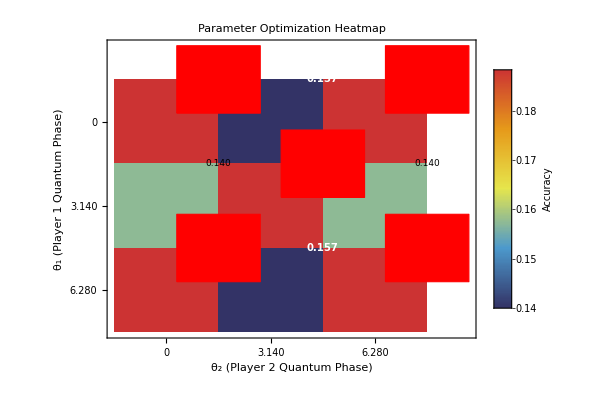

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
l1=1;
l2=1;
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,Pi/2,Pi/2,l1,l2]
```

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π/2, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.0113,ACQ1→0.0869,ACQ2→0.143,NEGO→0.1398,CAP1→0.0881,CAP2→0.0796,WAR1→0.2938,WAR2→0.1575,prediction→WAR1,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.0413,ACQ1→0.0114,ACQ2→0.3878,NEGO→0.1504,CAP1→0.0244,CAP2→0.1053,WAR1→0.1142,WAR2→0.1653,prediction→ACQ2,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.0117,ACQ1→0.1721,ACQ2→0.0406,NEGO→0.161,CAP1→0.1278,CAP2→0.0314,WAR1→0.3043,WAR2→0.1511,prediction→WAR1,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.139896

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = $Failed[bestTheta1] θ2 = $Failed[bestTheta2] λ1 = 1 λ2 = 1 | Accuracy = 0.139896

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1 | WAR2
ACQ1 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 1
ACQ2 | 5 | 80 | 0 | 0 | 0 | 0 | 0 | 14
CAP1 | 1 | 43 | 0 | 0 | 0 | 0 | 0 | 12
CAP2 | 10 | 71 | 0 | 0 | 0 | 0 | 0 | 18
NEGO | 4 | 75 | 0 | 0 | 0 | 0 | 0 | 20
SQ | 13 | 65 | 0 | 0 | 0 | 0 | 0 | 21
WAR1 | 3 | 73 | 0 | 0 | 0 | 0 | 0 | 23
WAR2 | 2 | 19 | 0 | 0 | 0 | 0 | 0 | 1

#### Setting 2: Lambda1 = 0.5 | Lambda2 = 0.5

```mathematica
datasetPath = "/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv" 
(* "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv"; *)
data=loadData[datasetPath];
```

/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Import::nffil: File /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv not found during Import.

Error: Could not load CSV file or file is empty

```mathematica
gridsize = 8;
l1 =0.5;
l2=0.5;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Error: Invalid data provided

Best parameters: θ1=$Failed[bestTheta1], θ2=$Failed[bestTheta2]

Best accuracy: $Failed[bestAccuracy]

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[$Failed]

```mathematica
visualizeGridSearchResults[gridResults]
```

Error: Input must be a grid search results Association with 'allResults' key

Use gridSearchQuantumThetas[] to generate proper grid search results

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Error: Invalid data passed to processQuantumDataset

```mathematica
getFirstNEntries[results,3]
```

Warning: resultAllData is empty

{}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Warning: No results to calculate accuracy from

Final Accuracy: 0.

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Warning: No results provided for confusion matrix

#### Setting 3: Lambda1 = 2 | Lambda2 = 2

```mathematica
datasetPath = "/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv";
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Import::nffil: File /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv not found during Import.

Error: Could not load CSV file or file is empty

```mathematica
gridsize = 8;
l1 =2;
l2=2;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Error: Invalid data provided

Best parameters: θ1=$Failed[bestTheta1], θ2=$Failed[bestTheta2]

Best accuracy: $Failed[bestAccuracy]

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[$Failed]

```mathematica
visualizeGridSearchResults[gridResults]
```

Error: Input must be a grid search results Association with 'allResults' key

Use gridSearchQuantumThetas[] to generate proper grid search results

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Error: Invalid data passed to processQuantumDataset

```mathematica
getFirstNEntries[results,3]
```

Warning: resultAllData is empty

{}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Warning: No results to calculate accuracy from

Final Accuracy: 0.

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Warning: No results provided for confusion matrix

#### Setting 4: Lambda1 = 0.1 | Lambda2 = 0.1

```mathematica
datasetPath = "/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv" ;
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Import::nffil: File /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv not found during Import.

Error: Could not load CSV file or file is empty

```mathematica
gridsize = 8;
l1 =0.1;
l2=0.1;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Error: Invalid data provided

Best parameters: θ1=$Failed[bestTheta1], θ2=$Failed[bestTheta2]

Best accuracy: $Failed[bestAccuracy]

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[$Failed]

```mathematica
visualizeGridSearchResults[gridResults]
```

Error: Input must be a grid search results Association with 'allResults' key

Use gridSearchQuantumThetas[] to generate proper grid search results

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Error: Invalid data passed to processQuantumDataset

```mathematica
getFirstNEntries[results,3]
```

Warning: resultAllData is empty

{}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Warning: No results to calculate accuracy from

Final Accuracy: 0.

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Warning: No results provided for confusion matrix

#### Setting 5: Lambda1 = 10 | Lambda2 = 10

```mathematica
datasetPath ="/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv" ;
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Import::nffil: File /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv not found during Import.

Error: Could not load CSV file or file is empty

```mathematica
gridsize = 8;
l1 =10;
l2=10;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Error: Invalid data provided

Best parameters: θ1=$Failed[bestTheta1], θ2=$Failed[bestTheta2]

Best accuracy: $Failed[bestAccuracy]

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[$Failed]

```mathematica
visualizeGridSearchResults[gridResults]
```

Error: Input must be a grid search results Association with 'allResults' key

Use gridSearchQuantumThetas[] to generate proper grid search results

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Error: Invalid data passed to processQuantumDataset

```mathematica
getFirstNEntries[results,3]
```

Warning: resultAllData is empty

{}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Warning: No results to calculate accuracy from

Final Accuracy: 0.

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Warning: No results provided for confusion matrix

#### Setting 6: Lambda1 = 0.0001 | Lambda2 = 0.0001

```mathematica
datasetPath ="/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv" ;
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Import::nffil: File /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv not found during Import.

Error: Could not load CSV file or file is empty

```mathematica
gridsize = 8;
l1 =0.0001;
l2=0.0001;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Error: Invalid data provided

Best parameters: θ1=$Failed[bestTheta1], θ2=$Failed[bestTheta2]

Best accuracy: $Failed[bestAccuracy]

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[$Failed]

```mathematica
visualizeGridSearchResults[gridResults]
```

Error: Input must be a grid search results Association with 'allResults' key

Use gridSearchQuantumThetas[] to generate proper grid search results

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Error: Invalid data passed to processQuantumDataset

```mathematica
getFirstNEntries[results,3]
```

Warning: resultAllData is empty

{}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Warning: No results to calculate accuracy from

Final Accuracy: 0.

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Warning: No results provided for confusion matrix

#### Setting 1: Lamda1 = 1 | Lambda2 = 1

```mathematica
datasetPath = "/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv"
(* "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv"; *)
data=loadData[datasetPath];
```

/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Import::nffil: File /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv not found during Import.

Error: Could not load CSV file or file is empty

```mathematica
gridsize = 9;
l1 =1;
l2=1;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Error: Invalid data provided

Best parameters: θ1=$Failed[bestTheta1], θ2=$Failed[bestTheta2]

Best accuracy: $Failed[bestAccuracy]

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[$Failed]

```mathematica
visualizeGridSearchResults[gridResults]
```

Error: Input must be a grid search results Association with 'allResults' key

Use gridSearchQuantumThetas[] to generate proper grid search results

```mathematica
l1=1;
l2=1;
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Error: Invalid data passed to processQuantumDataset

```mathematica
getFirstNEntries[results,3]
```

Warning: resultAllData is empty

{}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Warning: No results to calculate accuracy from

Final Accuracy: 0.

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Warning: No results provided for confusion matrix